## Centeroid-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 17:01:43
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

```mathematica
w=TemplateRandomSquareGrid[36, {-5,-5}, {5, 5}];
```

## Mark the centeroid of a single cell

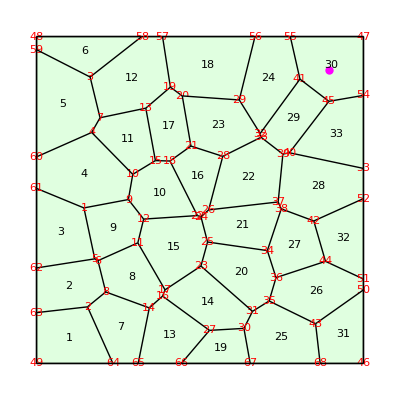

```mathematica
ShowTissue[w, "CellNumbers"-> True, "VertexNumbers"-> Red, Epilog-> {PointSize[.015], Magenta,Point[Centeroid[w,30]]}]
```

## Compare the centeroids and the centroids of all cells

```mathematica
cw=Centroid[w];
cew=Centeroid[w];
```

{{-4.02652,-4.17849},{-3.77751,-2.54346},{-4.19222,-0.941422},{-3.51849,0.716121},{-3.94641,2.85233},{-3.78551,4.59011},{-2.48628,-3.8763},{-1.94507,-2.49454},{-2.61783,-0.963208},{-1.38881,0.355921},{-2.28992,1.87613},{-1.98491,3.75638},{-0.973331,-4.0455},{0.176104,-3.17138},{-0.640555,-1.27704},{-0.0472257,0.480793},{-0.944248,2.24857},{0.0578486,3.93914},{0.649662,-4.47863},{1.39457,-2.28706},{1.24381,-0.6634},{1.55105,0.859246},{0.797625,2.19698},{2.1084,3.75835},{2.30187,-4.03426},{3.63573,-2.71506},{2.83825,-1.34206},{3.37536,0.412274},{2.66292,2.25292},{3.95237,3.9832},{4.30273,-4.13336},{4.32978,-1.223},{4.16937,2.1575}}

## Centroids in Blue Centeroids in Red

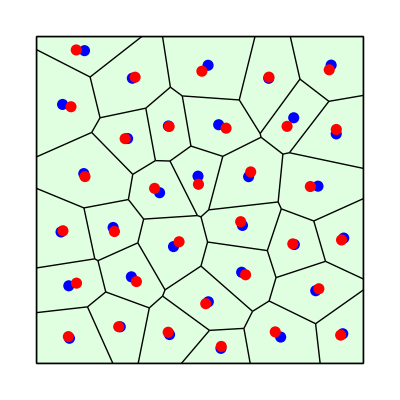

```mathematica
ShowTissue[w, Epilog-> {Blue, PointSize[.02], Point[cw], Red, Point[cew]}]
```

## Illustrate for a single polygon Centroid in Pink Centeroid in Blue

```mathematica
polygon = CellVertexCoordinates[w,15]
```

{{-1.90177,-1.31051},{-1.72383,-0.5841},{-0.0793609,-0.476342},{0.0297219,-0.514418},{0.231342,-1.28513},{0.0292848,-2.02062},{-1.06927,-2.74812}}

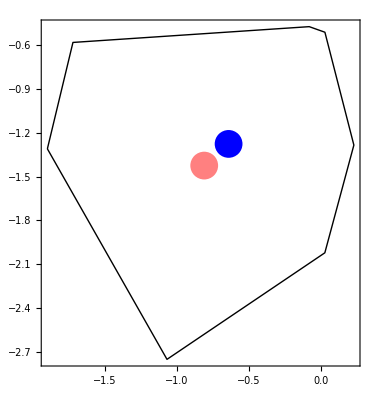

```mathematica
Show[Boundary[polygon], Graphics[{Pink, PointSize[.05], Point[Centroid[polygon]], Blue,Point[Centeroid[polygon]]}], Frame-> True]
```